# ABS Model with RW Wake (Solution to Dynamical System)

```mathematica
ClearAll["Global`*"]
$MachineEpsilon
$MachinePrecision
```

2.22045×10^-16

15.9546

```mathematica
$Assumptions=q∈Reals
size = 200/2;
```

q∈ℝ

```mathematica
(*Pre-calculated solution to RW wake*)
(*---RW square-well matrix element U_nm (all integers n,m incl.0)---*)
ClearAll[unm,unmBase,Sfac,Cfac];

(*Fresnel helper factors*)
Sfac[k_Integer?Positive]:=Sfac[k]=Sqrt[2/k] FresnelS[Sqrt[2 k]];
Cfac[k_Integer?Positive]:=Cfac[k]=Sqrt[2/k] FresnelC[Sqrt[2 k]];

(*
----Base formulas for nonnegative indices (nn,mm>=0)---- 
These are the analytic RW (W~1/Sqrt[s-s']) square-well results.
*)
unmBase[nn_Integer?NonNegative,mm_Integer?NonNegative]:=Which[
(*U_00=4/3*)
nn==0&&mm==0,4/3,
(*U_0m*)
nn==0&&mm>0,-(((-1)^mm)/(Pi *mm))*Sfac[mm],
(*U_n0*)
mm==0&&nn>0,-(1/(Pi nn))*Sfac[nn],
(*diagonal n=n>=1*)
nn==mm&&nn>0,(1/2)*(Cfac[nn]-(1/(Pi*nn))*Sfac[nn]),
(*off-diagonal for positive indices*)
nn>0&&mm>0,(1/(2 Pi))*((((-1)^(nn-mm))/(nn-mm)+((-1)^(nn+mm+1))/(nn+mm))*Sfac[mm]-((1/(nn-mm)+1/(nn+mm)))*Sfac[nn])];

(*----Full symmetry extension to all integers---- Uses:U_nm=U_|n||m|and U_nm=(-1)^(n-m) U_mn We implement by mapping to abs indices and using one triangle.*)
unm[n_Integer,m_Integer]:=Module[{nn=Abs[n],mm=Abs[m]},
Which[
nn==mm,unmBase[nn,mm],
nn>mm,unmBase[nn,mm],
True,(-1)^(nn-mm)*unmBase[mm,nn]
]
];
```

```mathematica
(* Define space charge and wake parameters to use *)
q=10.0;
w=2;
```

```mathematica
(* Build u matrix*)
umatrix = Table[unm[i,j],{i,-size,size,1},{j,-size,size,1}];//AbsoluteTiming
```

{0.976903,Null}

```mathematica
(* Build d matrix *)
dmatrix = Table[(n-q/2.)*KroneckerDelta[n,m]+(q/2.)*KroneckerDelta[-n,m],{n,-size,size,1},{m,-size,size,1}];//AbsoluteTiming
```

{0.04965,Null}

```mathematica
(* Build total matrix *)
mmatrix = -I*(dmatrix-w*umatrix);
```

```mathematica
(* Calculate eigenvectors and eigenvalues*)
{eigenvals,eigenvects}=Eigensystem[N[mmatrix]];//AbsoluteTiming
paired = Transpose[{eigenvals,eigenvects}];
(* Sort them by mode *)
sorted = SortBy[paired,-Im[First[#]] &];
{sortedVals,sortedVecs}=Transpose[sorted];
```

{0.029154,Null}

```mathematica
(* Get solutions and multiply by arbitrary constant tbd from initial conditions*)
sols = Exp[sortedVals*θ]*sortedVecs;
constants = Array[α,Length[sols]];
antheta = Total[sols*constants,{1}];
```

```mathematica
(* Get total solution including azimuthal solutions*)
azimuthalsols = Exp[1.*I*Range[-size,size]*ψ];
totalsol = Total[(antheta*azimuthalsols)];
(*Get expression at θ=0 to solve for constants *)
totalsolzero = Total[(antheta*azimuthalsols)/.{θ->0}];
```

```mathematica
(* Solve for constants with constant initial condition *)
initialcondition = 1.0;
ψVals=Subdivide[-Pi,Pi,2*size+1][[;;-2]];
equations=(ψVal↦(totalsolzero/. ψ->ψVal)==initialcondition)/@ψVals;//AbsoluteTiming
(*equations =Table[(totalsolzero/.{ψ->ψi})==initialcondition,{ψi,-Pi,Pi,2.*Pi/(2.*size+1)}];//AbsoluteTiming*)
initialsols = NSolve[equations,constants];//AbsoluteTiming
```

{2.17041,Null}

{58.6876,Null}

```mathematica
(* Build solutions *)
solution[θstar_,ψstar_]:= (totalsol/.initialsols)/.{θ->θstar,ψ->ψstar};
centroid[θstar_,ψstar_]:=(1/2)*(solution[θstar,ψstar]+solution[θstar,-ψstar]);
head[θstar_]:=Abs[centroid[θstar,0.0]];
tail[θstar_]:=Abs[centroid[θstar,Pi]];
headtailamplification [θstar_]:= Abs[centroid[θstar,Pi]]/Abs[centroid[θstar,0.0]];
```

```mathematica
(* Build ABS eigenfunctions *)
xl = Dot[sols,azimuthalsols];//AbsoluteTiming
xlcentroid = 0.5*(xl+(xl/.ψ->(-ψ)));
ns = 20;
xlcentroidstrobe =Table[Re[(xlcentroid[[i]]/.θ->0)*Exp[-2*I*Pi*j/ns]],{i,Length[xlcentroid]},{j,0,ns}];//AbsoluteTiming
```

{0.103553,Null}

{1.46125,Null}

```mathematica
(* Calculate amplification factors *)
xlPi=xl/. {ψ->Pi,θ->0};
xl0=xl/. {ψ->0,θ->0};
ks = Abs[xlPi/xl0];
(*kmax = Max[ks];*)
kmax=Max[ks];
kIndex = First@Ordering[ks,-1]-size-1;
logmax = Log[kmax];
```

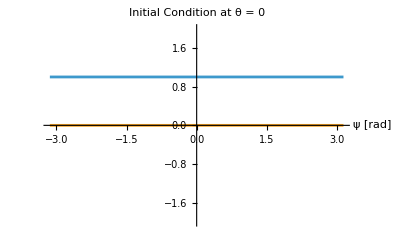

```mathematica
(* Plot initial condition *)
Plot[{Abs[solution[0,ψ]],Arg[solution[0,ψ]]},{ψ,-Pi,Pi},
AxesLabel->{Style["ψ [rad]", Black, Large]},
LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Initial Condition at θ = 0", Black, Larger], PlotLegends->{"",""},
PlotRange->{{-Pi,Pi},{-2,2}}, PlotPoints->10, PerformanceGoal->"Speed"]
```

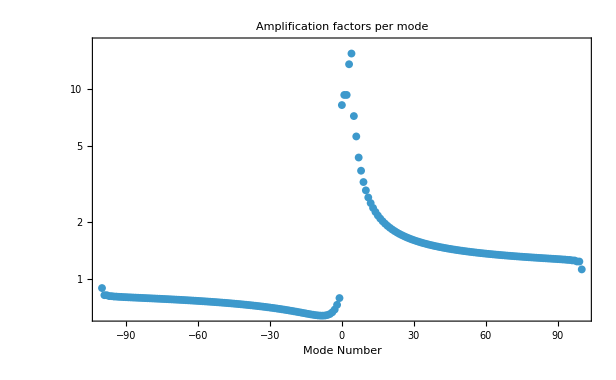

```mathematica
(* Plot amplification factors *)
ListLogPlot[Transpose[{Range[-size,size],ks}],PlotRange->{{Min[ks],kmax+2}},
Frame->{True,True,False,False},
FrameLabel->{Style["Mode Number", Black, Large],""}, LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Amplification factors per mode", Black, Larger], PerformanceGoal->"Speed"]
```

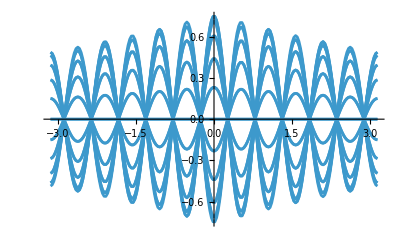
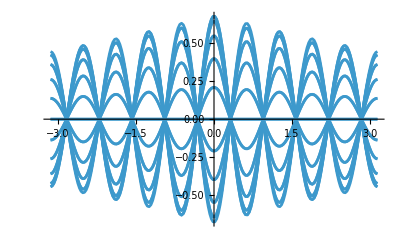
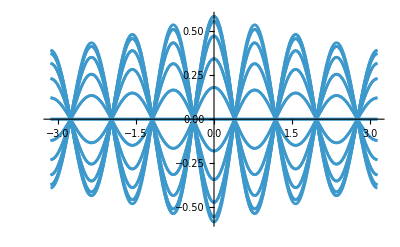
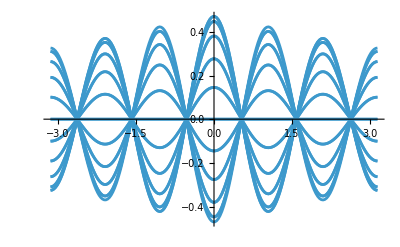
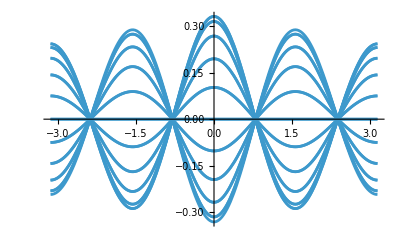
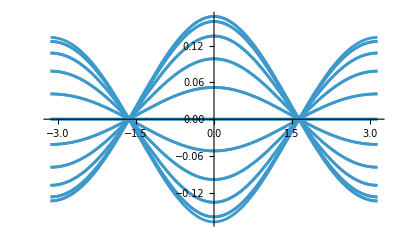
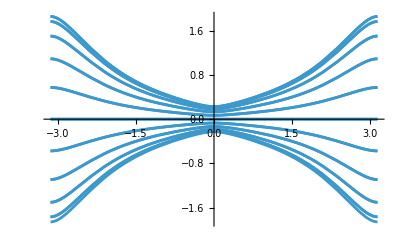
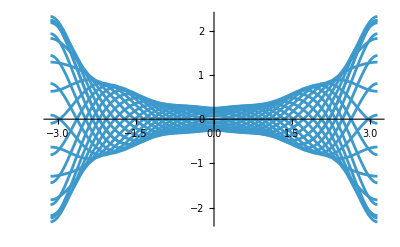

```mathematica
Table[Plot[Chop[xlcentroidstrobe[[size+i]]],{ψ,-Pi,Pi},PerformanceGoal->"Speed"],
{i,-5,5}
]
```

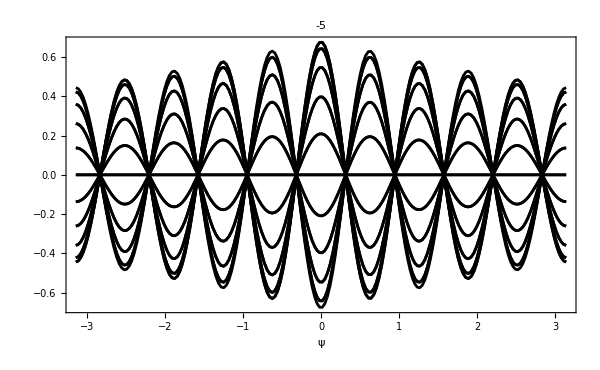
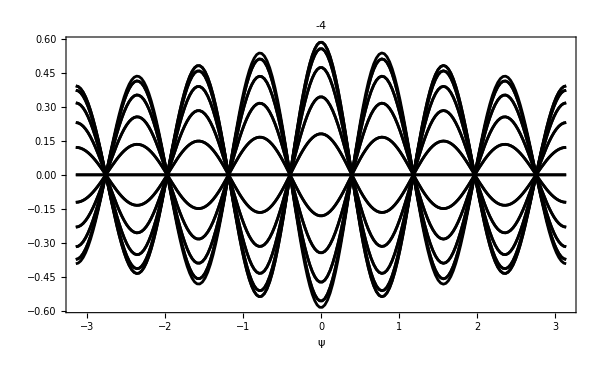
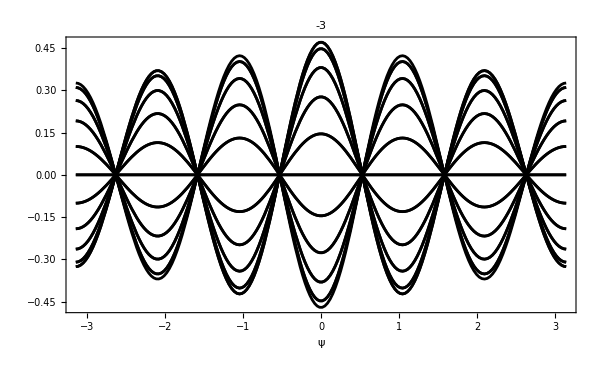
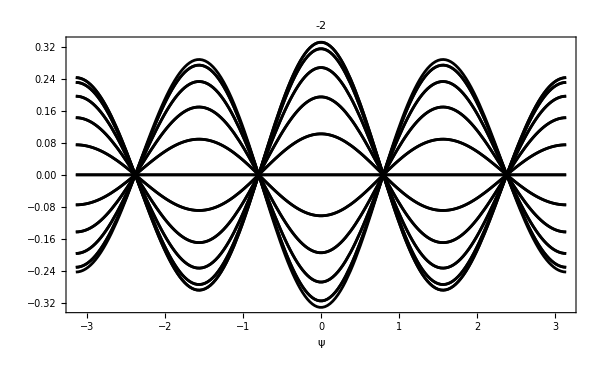
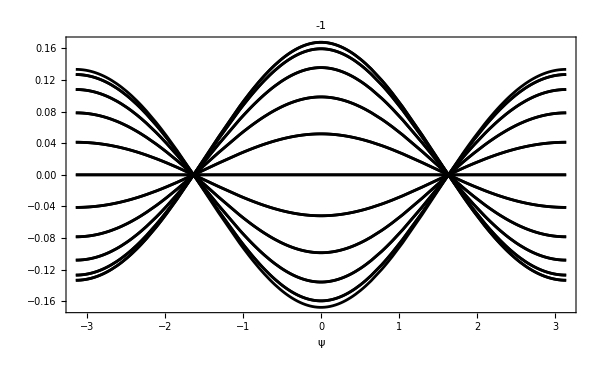
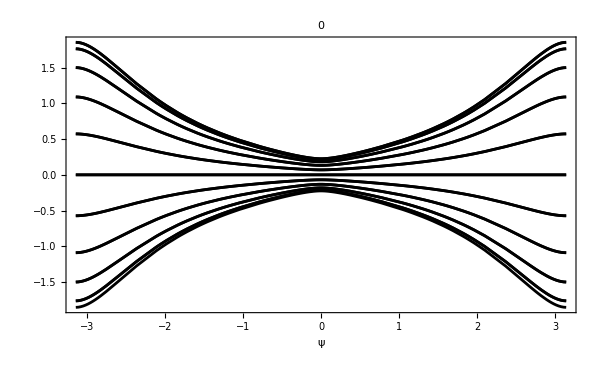
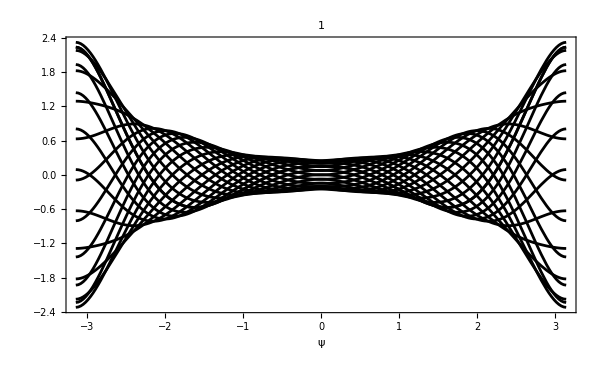
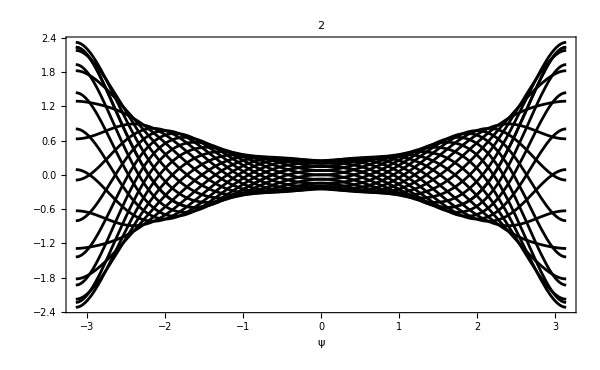

```mathematica
Table[Plot[Chop[xlcentroidstrobe[[size+i+1]]],{ψ,-Pi,Pi},PerformanceGoal->"Speed",
PlotStyle->{Black},
PlotLabel->Style[StringForm["`1`",i],Black],
FrameLabel->{ Style["ψ",45,Black],Style["",45,Black]},
FrameStyle->Black,Frame->True,ImageSize->600,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30}],
{i,-5,5}
]
```